```mathematica
dowJonesMember={"MMM","AXP","AAPL","BA","CAT","CVX","CSCO","KO","DD","XOM","GE","GS","HD","INTC","IBM","JNJ","JPM","MCD","MRK","MSFT","NKE","PFE","PG","TRV","UNH","UTX","VZ","WMT","DIS"};
```

```mathematica
trainingSet=rawFeatures[2000,2008]/@dowJonesMember;
```

```mathematica
trainingReturns=r[2000,2008]/@dowJonesMember;
trainingReturns=Flatten[trainingReturns,1];
```

```mathematica
rawFeaturesMatrix=Flatten[trainingSet,1];
```

```mathematica
augmentedTrainingSet=augmentFeaturesMatrix[1.,1.,n1,n2,n3][rawFeaturesMatrix]
```

{1}
 |  |  |  |

```mathematica
{normalizedTrainingFeatures,A,b}=Φ[augmentedTrainingSet];
```

```mathematica
q=findQ[0,1,normalizedTrainingFeatures,trainingReturns]
```

```mathematica
Dimensions[normalizedTrainingFeatures]
```

{58261,65}

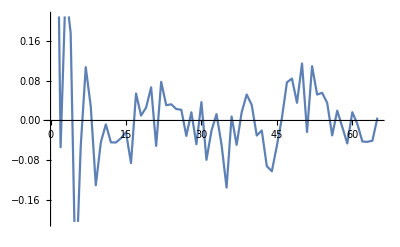

```mathematica
ListLinePlot[q]
```